```mathematica
Clear[h];
R=0.17;
c=340;
t0=R/c;
coef[nmax_,n_]:=nmax! (nmax+1)!/(nmax+n+1)!/(nmax-n)!;
coef2[nmax_,n_]:=nmax! nmax!/(nmax+n)!/(nmax-n)!;
h[n_,t_]:=Sqrt[2 n+1]*(LegendreP[n,t/t0] UnitStep[t+t0] UnitStep[-t]+Cos[t/t0] LegendreP[n,Sin[t/t0]] UnitStep[t] UnitStep[π/2 t0-t])
h2[n_,t_]:=If[Mod[n,2]==0,Cos[n ArcSin[t/t0]]/Sqrt[t0*t0-t*t]* UnitStep[t+t0] UnitStep[-t]+Cos[n t/t0] /t0 UnitStep[t] UnitStep[π/2 t0-t],-Sin[n ArcSin[t/t0]]/Sqrt[t0*t0-t*t]* UnitStep[t+t0] UnitStep[-t]-Sin[n t/t0] /t0 UnitStep[t] UnitStep[π/2 t0-t]];
harmonic2[n_,a_]:=If[Mod[n,2]==0, Cos[n a],Sin[n a]];
perceivedTimeDomain[nmax_,t_]:=Sum[h[n,t]  ,{n,0,nmax}];
perceivedTimeDomain2[nmax_,t_]:=Sum[h2[n,t] coef2[nmax,n] harmonic2[n,π/2],{n,0,nmax,2}];
```

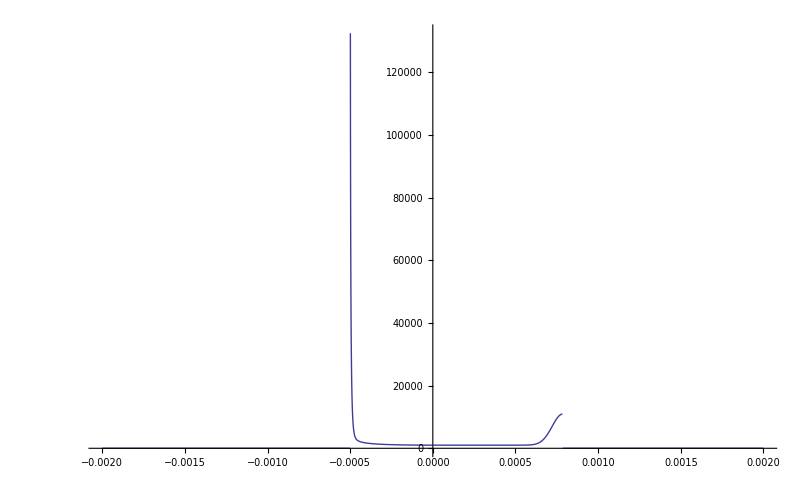

```mathematica
a=Plot[perceivedTimeDomain2[125,t],{t,-4*t0,4 t0},PlotRange->All]
```

```mathematica
Table[LegendreP[n,1],{n,0,10}]
```

{1,1,1,1,1,1,1,1,1,1,1}

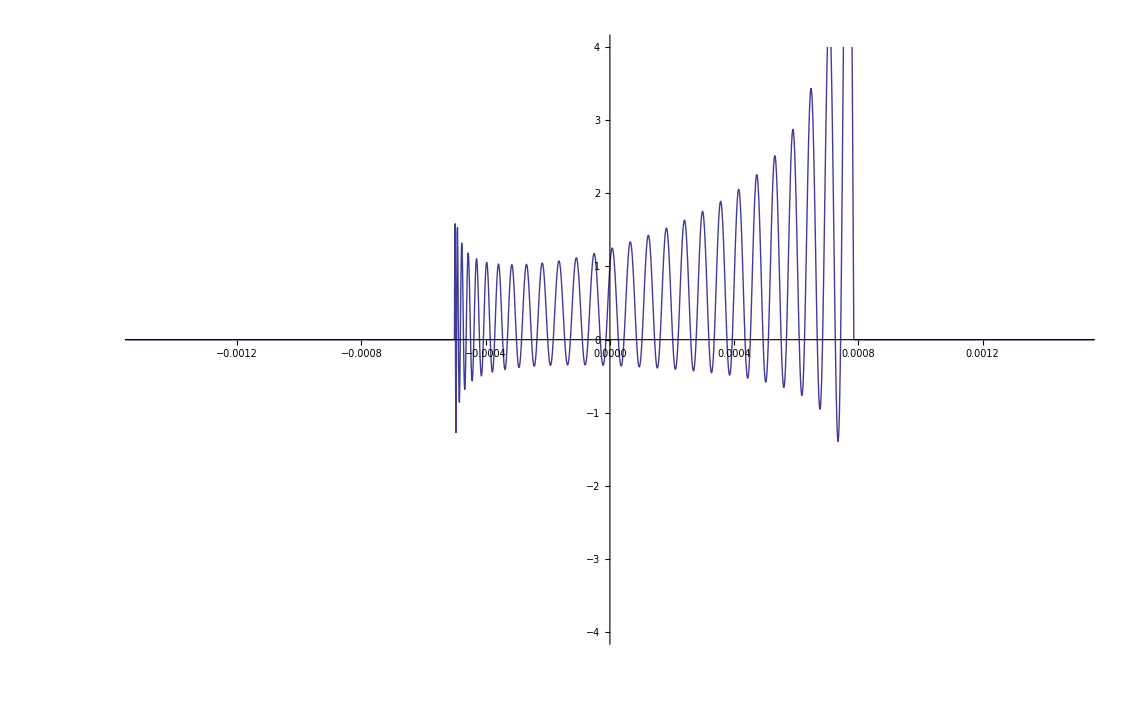

```mathematica
a=Plot[perceivedTimeDomain[3,t],{t,-4*t0,4 t0},PlotRange->{{-3*t0,3*t0},{-4,4}}]
```

```mathematica
b=Plot[perceivedTimeDomain[23,t],{t,-4*t0,4 t0},PlotRange->{{-3*t0,3*t0},{-4,4}}]
```

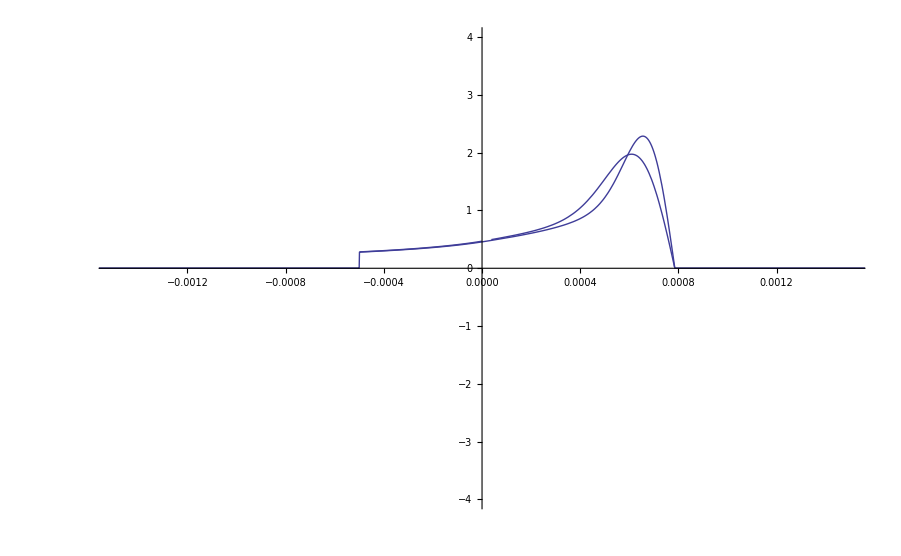

```mathematica
Show[a,b]
```

-Graphics-

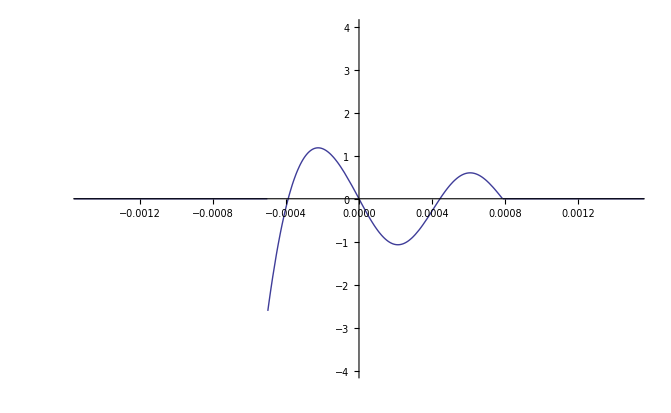

```mathematica
Plot[h[3,t],{t,-4*t0,4 t0},PlotRange->{{-3*t0,3*t0},{-4,4}}]
```

```mathematica
Fs=44100;
extension = 32;
tmin = -extension t0; tmax= extension t0;
dt=1./Fs;
nPoints = Round[(tmax-tmin)/dt];
hdiscrete[n_]:=Table[h[n,tmin + i*dt],{i,0,nPoints}]
hdiscrete2[n_]:=Table[h2[n,tmin + i*dt],{i,0,nPoints}]
hw[n_]:=Fourier[hdiscrete[n]];
hw2[n_]:=Fourier[hdiscrete2[n]];
perceivedw[nmax_]:=Sum[hw[n] coef[nmax,n],{n,0,nmax}];
perceivedw2[nmax_]:=Sum[hw2[n] coef2[nmax,n],{n,0,nmax}];
```

```mathematica
Table[LegendreP[n,1],{n,0,10}]
```

{1,1,1,1,1,1,1,1,1,1,1}

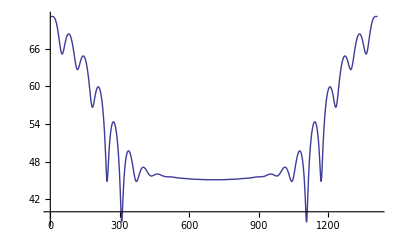

```mathematica
order=320;
a=ListPlot[20*Log[10,Abs[perceivedw2[order]]],Joined->True, PlotRange->All];
b=ListPlot[20*Log[10,Abs[hw2[order]]],Joined->False, PlotRange->{{0,nPoints/2},{-50,10}}];
Show[a]
```

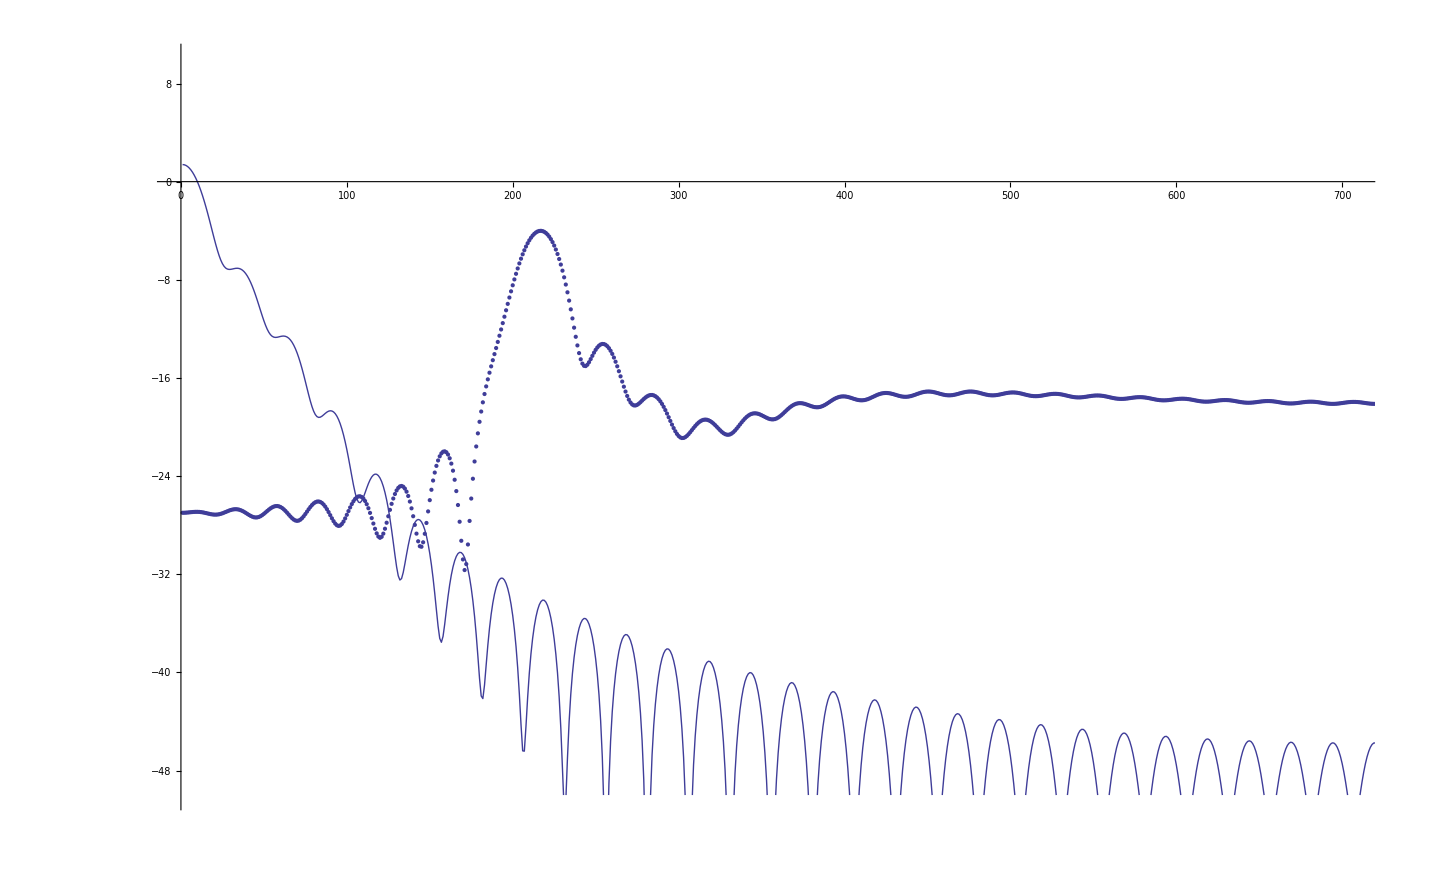

```mathematica
order=20;
a=ListPlot[20*Log[10,Abs[perceived[order]]],Joined->True, PlotRange->{{0,nPoints/2},{-50,10}}];
b=ListPlot[20*Log[10,Abs[hw[order]]],Joined->False, PlotRange->{{0,nPoints/2},{-50,10}}];
Show[a,b]
```